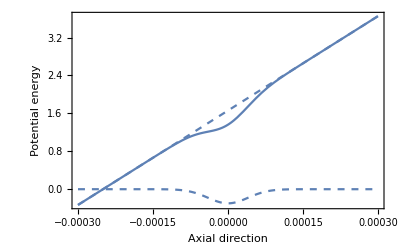

0.715877

```mathematica
Clear[r]
Clear[z]
Clear[rmin]
a=(55+23)/1000; (*55mm is inner radius and the outer radius is 55+46 mm*)
current=50;                                               (*current in A*)
coil=108;
d=(110+25)/1000; (*2*55mm radius + 25 extension along axial*)
da=1;(*change in radius*)
range=150/1000;
alpha=r/rmin;
beta=z/rmin;
gamma=z/r;
Q=((1+alpha)^2+beta^2);
k=(4alpha/Q)^0.5;
r=0;                                                                (*coil depth*)
B=10^(-7)*coil*current*4Pi/(2rmin);

F[r_,z_,rmin_]=B(1/(Pi(Q^0.5)))(EllipticE[k*k]((1-alpha^2-beta^2)/(Q-4alpha))+EllipticK[k*k]);
G1[r_,z_,rmin_]=F[r,z-d/2,rmin]-F[r,z+d/2,rmin];
Plot[G1[0,z,a],{z,-range,range}];

g=250*10^(-6);

P=3; (*Power*)
w=80*10^(-6);(*Beam waist*)
range=300*10^-6;
epsilon=8.845*10^(-12);alpha=5.3*10^(-39);c=3*10^8;
U=(4*alpha*P)/(4*Pi*epsilon*c*w*w);
bohr=9.274*10^(-24);
gs=2;S=1/2;L=0;gl=1;
mu=-gs*bohr*S-gl*bohr*L;

p1=Plot[-(U*Exp[-2(z/w)^2])*10^27,{z,-range,range},PlotRange->All,PlotStyle->Dashed,PlotLegends->"ODT",Frame->True,AxesLabel->{"Axial direction","Potential energy"}];
p2=Plot[-mu*G1[0,z+g,a]*10^27,{z,-range,range},PlotRange->All,PlotStyle->Dashed,PlotLegends->"MagneticPotential",Frame->True,AxesLabel->{"Axial direction","Potential energy"}];
p4=Plot[-(U*Exp[-2(z/w)^2])*10^27-mu*G1[0,z+g,a]*10^27,{z,-range,range},PlotRange->All,PlotStyle->Thick,Frame->True,PlotLegends->"Both",AxesLabel->{"Axial direction","Potential energy"}];
Show[p1,p2,p4]
(G1[0,w,a]-G1[0,-w,a])/(2*w)
```

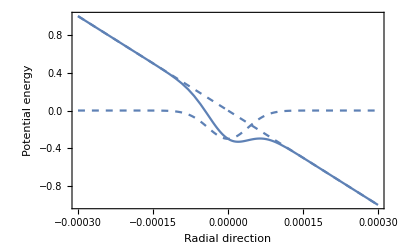

0.357938

```mathematica
Clear[r]
Clear[z]
Clear[rmin]
a=(55+23)/1000; (*55mm is inner radius and the outer radius is 55+46 mm*)
current=50;                                               (*current in A*)
coil=108;
d=(110+25)/1000; (*2*55mm radius + 25 extension along axial*)
da=1;(*change in radius*)
range=150/1000;
alpha=r/rmin;
beta=z/rmin;
gamma=z/r;
Q=((1+alpha)^2+beta^2);
k=(4alpha/Q)^0.5;
B=10^(-7)*coil*current*4Pi/(2rmin);

Fr[r_,z_,rmin_]=gamma*B(1/(Pi(Q^0.5)))(EllipticE[k^2]((1+alpha^2+beta^2)/(Q-4alpha))-EllipticK[k^2]);
Gr[r_,z_,rmin_]=Fr[r,z-d/2,rmin]-Fr[r,z+d/2,rmin];
Plot[Gr[r,0,a],{r,-range,range}];

g=250*10^(-6);

P=3; (*Power*)
w=80*10^(-6);(*Beam waist*)
range=300*10^-6;
epsilon=8.845*10^(-12);alpha=5.3*10^(-39);c=3*10^8;
U=(4*alpha*P)/(4*Pi*epsilon*c*w*w);
bohr=9.274*10^(-24);
gs=2;S=1/2;L=0;gl=1;
mu=-gs*bohr*S-gl*bohr*L;

p1=Plot[-(U*Exp[-2(r/w)^2])*10^27,{r,-range,range},PlotRange->All,PlotStyle->Dashed,PlotLegends->"ODT",Frame->True,AxesLabel->{"Radial direction","Potential energy"}];
p2=Plot[-mu*Gr[r,0+g,a]*10^27,{r,-range,range},PlotRange->All,PlotStyle->Dashed,PlotLegends->"MagneticPotential",Frame->True,AxesLabel->{"Radial direction","Potential energy"}];
p4=Plot[-(U*Exp[-2(r/w)^2])*10^27-mu*Gr[r,0+g,a]*10^27,{r,-range,range},PlotRange->All,PlotStyle->Thick,Frame->True,PlotLegends->"Both",AxesLabel->{"Rdial direction","Potential energy"}];
Show[p1,p2,p4]
-(Gr[w,g,a]-Gr[-w,g,a])/(2*w)
```